# Simulation algorithm tests

### This notebook compares simulations for dt=2^-5, 2^-6 (standard) and 2^-7 It uses CIP data because it represents “middle ground” between RIF (high mutation rate) and STR (low mutation rate) and thus is a reasonable compromise between getting a good statistics (P_regrowth) and sensitivity to approximations (P_regrowth neither too close to zero nor one)

## Helper functions

```mathematica
SetDirectory[NotebookDirectory[]]

ksround=0.01; (* round-off parameters for the KS test for the least-frequent strain data *)

SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[DispPval]
DispPval[p_]:=Which[p<0.001,"<0.001",p<0.01,ToString[NumberForm[p,{2,4}]],p<0.1,ToString[NumberForm[p,{2,3}]],p<1,ToString[NumberForm[p,{2,2}]]]

SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram,BarChart,Graphics},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];

Clear[NaiveMinimization,testf]
testf[x_]:=(x-3 10^-9)^2
NaiveMinimization[fun_,a0_,b0_,ϵ_]:=Module[{a,b,c,d,fa,fb,fc,fd,gr=1.(Sqrt[5]+1)/2},a=1.a0;b=1.b0;Do[
c=b-(b-a)/gr;
d=a+(b-a)/gr;
fa=fun[a];fb=fun[b];fc=fun[c];fd=fun[d];
If[fc<fd,b=d;fb=fd,a=c;fa=fc];
Print[a," ",b, " fa=",fc," fb=",fb];
If[(b-a)<ϵ,Break[]]
,{n,10}];
Return[(a+b)/2]]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor

## Data import and model parameters:

```mathematica
<<("turb_cip_long_runs_ODvsTIME.mx");
dataCIPlong=data;
Length[dataCIPlong]

CIPtimestopfilamenting=2.0;(* value should be the same as the one used in the spike-in modelling notebook *)

<<("turb_cip_long_runs.mx");
paramsCIPlong=alldata;

<<("turb_cip_short_runs.mx")
paramsCIPshort=alldata;
Print[Length[paramsCIPshort[[1]]]]

experfractions=Select[1.{n,0,n,n, 0,21/(21+76),9/(59+9),n, 0,0,n,0, n,0,n,n,n,n,0,0,n,n,n,0,  0,n,0,1/(1+32+58+51+62)},(NumberQ[#])&] (* n = no regrowth *)
cfus={8,9,8,5,   4,11,2,25,   34,6,4,5,   4,8,18,5,   26,12,11,0};

tmax=30;
odcrit=0.1;
odregrowth=0.05;dilf=0.75;

(* for plotting and simulations *)
tregrowthbin={10,26,2};
tregrowthpmax=0.25;
cfusbin={0,40,2};
cfuspmax=0.25;
noreps="1000" ;(* number of replicate simulations *)
```

32

20

{0.,0.,0.216495,0.132353,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00490196}

## Plotting functions

```mathematica
colors={Darker[Green],Darker[Red],Blue,Darker[Yellow],Darker[Magenta],Pink}
```

{RGBColor[0, Rational[2, 3], 0],RGBColor[Rational[2, 3], 0, 0],RGBColor[0, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[Rational[2, 3], 0, Rational[2, 3]],RGBColor[1, 0.5, 0.5]}

```mathematica
Clear[MakeBar2,MakeBarFromNM,RegrowthProbPlot,RegrowtTimeDistribution,LeastAbundantStrain]
MakeBar2[x_,y1_,y2_]:={AbsolutePointSize[10],Point[{x,(y1+y2)/2}],AbsoluteThickness[2],Line[{{x-0.25,y1},{x+0.25,y1}}],Line[{{x-0.25,y2},{x+0.25,y2}}],AbsoluteThickness[1],Line[{{x-0.15,y1},{x+0.15,y1}}],Line[{{x-0.15,y2},{x+0.15,y2}}],Line[{{x,y1},{x,y2}}]};
MakeBarFromNM[x_,n_,m_]:=MakeBar2[x,(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]]/.z->1 (* Wilson score interval https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval *)
RegrowthProbPlot[names_]:=Module[{gr,pexp,pth,simdist,tmp={},tmp2},
Do[
simdist=Table[Import["models\\"<>names[[j]]<>"\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp2=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp2=Flatten[tmp2,1];
pth=Length[Select[tmp2,NumberQ[#1⟦2⟧]&]]/Length[tmp2];
Print["conf. intervals: ",{1.(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],1.(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]}/.{z->1,n->Length[tmp2],m->Length[Select[tmp2,(NumberQ[#[[2]]]&)]]}];
AppendTo[tmp,tmp2];
,{j,Length[names]}];

pexp=Length[Select[tregrowths,NumberQ[#1]&]]/Length[tregrowths];

gr=Graphics[Flatten[{MakeBarFromNM[0.7,Length[tregrowths],Length[Select[tregrowths,NumberQ[#]&]]],Table[{colors[[i]],MakeBarFromNM[0.7+0.8i,Length[tmp[[i]]],Length[Select[tmp[[i]],(NumberQ[#[[2]]]&)]]]},{i,Length[tmp]}]}],(*Epilog->{Text["g_s",{0.7,0}],Text["g_r",{1.5,0}]},*)Axes->{None,Automatic},PlotRange->{{0,1.2+0.8Length[tmp]},{0,1}},Axes->True,Frame->False,AxesLabel->{None,"P_regrowth"},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AspectRatio->1.3,ImageSize->200];
Print[gr];
(*Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"]*)]

RegrowtTimeDistribution[names_]:=Module[{gr,pval,grs,grexp,tmp,th},
grs={Histogram[Select[tregrowths-ainjs,(#≠∞)&],tregrowthbin,"PDF",ChartStyle->Opacity[0.5,Black]]};
Do[
simdist=Table[Import["models\\"<>names[[j]]<>"\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
th=Select[tmp,((NumberQ[#[[2]]])&)][[All,2]];
AppendTo[grs,SmoothHistogram[th,Automatic,"PDF",PlotStyle->colors[[j]]]];
Print["Mean time = ",Mean[th]," +/- ",SE[th]]
,{j,Length[names]}];

gr=Show[grs(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->200(*,ChartLegends->{"sim","exp"}*),PlotRange->{0,tregrowthpmax}];
Print[gr];
(*Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];*)
]

LeastAbundantStrain[]:=Module[{fractions,gr},
If[Length[simdist[[1,1]]]==8,
fractions=Table[Min[1.#[[6]]/(#[[8]]+#[[6]]),1.#[[8]]/(#[[8]]+#[[6]])]&/@Select[simdist[[i]],(#[[6]]+#[[8]]>0)&],{i,Length[simdist]}]
,If[Length[simdist[[1,1]]]==10,fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}],Print["incorrect format"];Abort[]]];
gr=Histogram[{Flatten[fractions],experfractions},{0,0.5,0.1},"PDF",ScalingFunctions->{"Linear","Linear"},PlotRange->All,ChartStyle->{Darker[Green],Black},Frame->True,FrameTicks->{{{0,2,4,6,8},Automatic},{{0,0.25,0.5},Automatic}},FrameLabel->{"fraction",None(*"PDF"*)},ImageSize->200,(*ChartLegends->{"sim","exp"},*)AspectRatio->1,PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]]]),24]];
Print[gr];
(*Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];*)
Print["fraction below 0.1 (exp):",1.Length[Select[experfractions,(#<0.1)&]]/Length[experfractions]];
Print["fraction below 0.1 (sim):",1.Length[Select[Flatten[fractions],(#<0.1)&]]/Length[Flatten[fractions]]];
]

Clear[FisherExactTest]
FisherExactTest[succ1_,n1_,succ2_,n2_]:=1.(n1! n2! (n1+n2-succ1-succ2)! (succ1+succ2)!)/((n1+n2)! (n1-succ1)! succ1! (n2-succ2)! succ2!)

Clear[HistogramMutants]

HistogramMutants[namepart_,strains_,alleles_,range_:{{0,cfusbin[[2]]},{0,cfuspmax}}]:=Module[{types=Table[Number,{strains*(alleles+1)}],simcfus,thcfus},
(* this simpler method ignores fitting the tfirstthr times, but works nevertheless and is much faster *)
simcfus=Table[ReadList[namepart<>ToString[n]<>".dat",types],{n,Length[births2]}];
Print[Length[simcfus]];
thcfus=Select[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],(#<=Max[cfus])&];
pl=Show[{Histogram[cfus,cfusbin,"PDF",ChartStyle->Gray],SmoothHistogram[thcfus,Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom,Frame->True,FrameLabel->{"n_r",None(*"PDF"*)},PlotRange->range]},PlotRange->range,AspectRatio->1,ImageSize->200,PlotLabel->Style[
"p_value= "<>DispPval[KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus]]
,24]];
Print[pl];
(*Export[output,pl,"PNG"]*)
]
```

### The fitting function that will be maximized when fitting the model to three data types:

```mathematica
Clear[FittingFunction]
FittingFunction[pval1_,pval2_,pval3_]:=pval1-If[pval2<0.1,100(0.1-pval2),0]-If[pval3<0.1,100(0.1-pval3),0]  (* same as for RIF *)
```

## Simple model for CIP. One resistant allele. No filamentation. Mixed strains AD30 and AD30YFP.

### Long - term experiment

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIPlong;
Length[vols]
Do[If[birthsres[[i,1]]==0,tregrowths[[i]]=∞],{i,Length[births]}]
tregrowths
Print["mean time to regrowth = ",Max[Select[tregrowths,NumberQ]]]
Print["max. time to end = ",Max[Select[tends,NumberQ]]]
```

32

{∞,22.0496,∞,∞,20.3132,21.9364,22.7454,∞,21.7159,24.4248,∞,21.5132,∞,22.553,∞,∞,∞,∞,23.7273,19.657,∞,∞,∞,23.9676,27.4156,∞,21.3304,18.369,∞,∞,∞,26.0315}

mean time to regrowth = 27.4156

max. time to end = 30.1147

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2 && Abs[#]>0)&])[[All,1,1]]
```

{2,5,6,7,9,10,12,14,19,20,24,25,27,28,32}

### We use the same code as for the multi-allele model below, but set the number of alleles = 1:

```mathematica
mutrate="1.2e-9";  (* value from fluctuation test for AD30 and EEL02 *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt5\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"];
Export[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt7\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"];
Export[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt10\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

1.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt5"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt5.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt7"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt7.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\alg_tests_CIP_dt5

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt5.exe 32 13 fixed_mu_2strains_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_32.dat 0.1

0

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\alg_tests_CIP_dt7

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt7.exe 32 13 fixed_mu_2strains_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_32.dat 0.1

0

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt10"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt10.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\alg_tests_CIP_dt10

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt10.exe 32 13 fixed_mu_2strains_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_32.dat 0.1

0

conf. intervals: {0.609507,0.619902}

conf. intervals: {0.599377,0.609536}

conf. intervals: {0.597167,0.607411}

conf. intervals: {0.59752,0.607839}

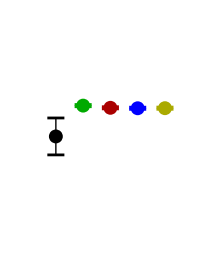

```mathematica
RegrowthProbPlot[{"alg_tests_CIP_dt5","CIP","alg_tests_CIP_dt7","alg_tests_CIP_dt10"}]
(*RegrowtTimeDistribution[]
LeastAbundantStrain[]*)
```

Mean time = 16.7951 +/- 0.0342332

Mean time = 16.8485 +/- 0.0343953

Mean time = 16.8037 +/- 0.0349518

Mean time = 16.8485 +/- 0.0343953

Mean time = 16.7839 +/- 0.0357127

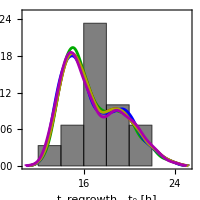

```mathematica
RegrowtTimeDistribution[{"alg_tests_CIP_dt5","CIP","alg_tests_CIP_dt7","CIP","alg_tests_CIP_dt10"}]
```

# FINISHED HERE

### Short - term experiment:

```mathematica
{vols2,births2,odinis2,tfirstthr2,tends2}=paramsCIPshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
```

20

### μ = 1.2 x 10^-9 does not fit the short term experiment. The code below shows this mismatch.

```mathematica
mutrate="1.2e-9";
```

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt5\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"];
Export[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt7\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

1.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt5"]
args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt5.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt7"]
args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt7.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\alg_tests_CIP_dt5

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt5.exe 20 13 preexist_res_2strains_1_allele_1.2e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat  0.1

0

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\alg_tests_CIP_dt7

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_dt7.exe 20 13 preexist_res_2strains_1_allele_1.2e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_1_allele_1.2e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat  0.1

0

20

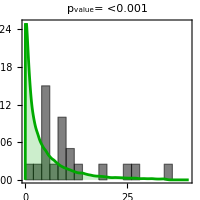

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\alg_tests_CIP_dt7\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_CIP",strains,alleles]
```

# finished here

### Find the optimal μ that maximizes the p - value of the fit to the pre-CIP mutant distribution:

```mathematica
Clear[RunOnce,mu]
RunOnce[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\CIP"];

args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth]," 100 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];

ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)


simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus];
Return[-pval]]
```

```mathematica
NaiveMinimization[RunOnce,2 10^-9,4 10^-9,10^-10]
```

2.×10^-9 3.23607×10^-9 fa=-0.555236 fb=-0.18557

2.47214×10^-9 3.23607×10^-9 fa=-0.302428 fb=-0.18557

2.47214×10^-9 2.94427×10^-9 fa=-0.555236 fb=-0.444311

2.65248×10^-9 2.94427×10^-9 fa=-0.389037 fb=-0.444311

2.76393×10^-9 2.94427×10^-9 fa=-0.555236 fb=-0.444311

2.76393×10^-9 2.87539×10^-9 fa=-0.590177 fb=-0.544129

2.8065×10^-9 2.87539×10^-9 fa=-0.579164 fb=-0.544129

2.84095×10^-9

### μ = 2.8 x 10^-9 fits the data best

## Now the same simple model, but with filamentation. Same old μ=1.2 x 10^-9 from the fluctuation test (which we already know does not fit mutant number distribution)

```mathematica
mutrate="1.2e-9";  (* value from fluctuation test for AD30 and EEL02 *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\CIP_filament\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

1.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 32 13 fixed_mu_2strains_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 1.2e-9 1.2e-9 0.75 input_params_32.dat 0.1

0

0.42926

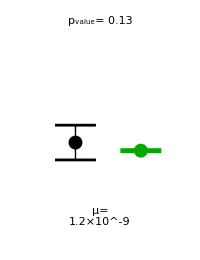

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_2allele_no_lag_Pregrowth.png

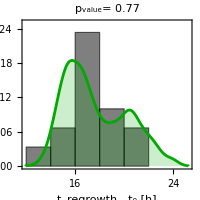

KS-test p-value: 0.770418

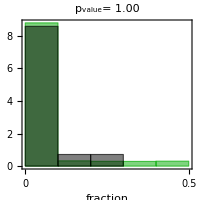

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.878548

```mathematica
simdist=Table[Import["models\\CIP_filament\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_filam_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_filam_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_filam_2allele_no_lag_LBS.png"]
```

## Single allele model for CIP with μ fitted to the mutant distribution data No filamentation just yet.

```mathematica
mutrate="2.8e-9";  
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\CIP_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

2.8×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_fitted"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_fitted

0.880341

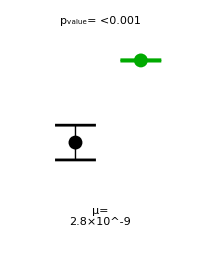

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_fitted_2allele_no_lag_Pregrowth.png

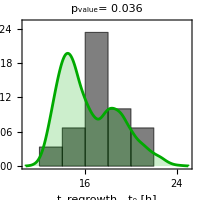

KS-test p-value: 0.0364892

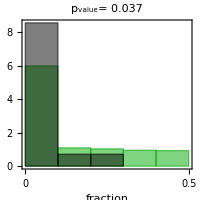

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.599469

```mathematica
simdist=Table[Import["models\\CIP_fitted\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_fitted_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_fitted_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_fitted_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\CIP_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_fitted"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]


SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 20 13 preexist_res_2strains_1_allele_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1

0

20

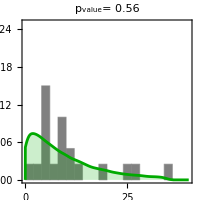

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_fitted_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_fitted\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_CIP",strains,alleles,NotebookDirectory[]<>"\\figures\\CIP_fitted_2allele_no_lag_Nmut.png"]
```

## Now the same with filamentation: Single allele model for CIP fitted to the mutant distribution data

```mathematica
mutrate="2.8e-9";  (* value fitted to the mutant distribution data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\CIP_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

2.8×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_fitted"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament_fitted

0.725768

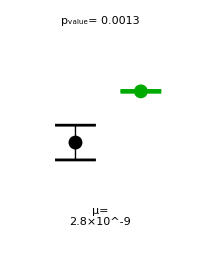

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_fitted_2allele_no_lag_Pregrowth.png

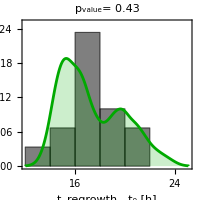

KS-test p-value: 0.432109

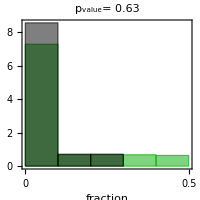

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.729288

```mathematica
simdist=Table[Import["models\\CIP_filament_fitted\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_filam_fitted_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_filam_fitted_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_filam_fitted_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\CIP_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_fitted"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 20 13 preexist_res_2strains_1_allele_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_1_allele_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1

0

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_filament_fitted\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_CIP",strains,alleles,NotebookDirectory[]<>"\\figures\\CIP_filam_fitted_2allele_no_lag_Nmut.png"]
```

20

-Graphics-

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_fitted_2allele_no_lag_Nmut.png

## Multi-allele model for CIP. Mixed strains AD30 and AD30YFP.

### Long - term evolutionary experiment

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&];
DumpSave[NotebookDirectory[]<>"\\CIP_mult_alleles.mx",allrates]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];

LBrates
CIPrates

mutrate="2.8e-9";  (* this value must be chosen to give the best fit to all data: regrowth times, CFUs, etc *)
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]


BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};

Export["models\\CIP_mult\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

{{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

{{0.,4.},{1.,0.},{2.,3.},{0.,4.},{0.,1.},{2.,1.},{1.,0.},{1.,0.},{1.,0.},{0.,4.},{2.,3.},{4.,4.},{0.,1.}}

{1.43438,1.53978,1.39731,1.05029,1.12944}

{1.91654,1.85083,1.98136,1.83286,1.24441}

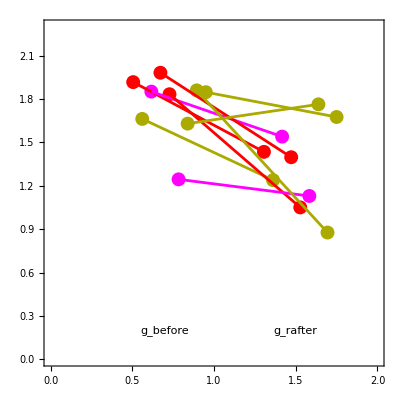

```mathematica
mutantorigin=Import["mutation_summary_turbidostat.xlsx","XLSX"][[2,2;;]];
mutantgrowthrates=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1,2;;]];
nosdetected=(mutantorigin[[Position[mutantorigin,#][[1,1]]]][[2;;3]])&/@mutantgrowthrates[[4;;,3]]
CIPratesTurbidostat=Select[Table[If[nosdetected[[i,2]]>0,CIPrates[[i]],0],{i,9}],(#>0)&]
LBratesTurbidostat=Select[Table[If[nosdetected[[i,2]]>0,LBrates[[i]],0],{i,9}],(#>0)&]

colors=Table[If[nosdetected[[i,1]]>0,If[nosdetected[[i,2]]>0,Magenta,Darker[Yellow]],Red],{i,alleles}];
Clear[MakePoints]
MakePoints[x_,data_]:={AbsolutePointSize[10],Table[{colors[[i]],Point[{x+(i/Length[data]-0.5)0.5,data[[i]]}]},{i,Length[data]}]}
Show[Graphics[{MakePoints[0.7,LBrates],MakePoints[1.5,CIPrates]},Epilog->{Text["g_before",{0.7,0.2}],Text["g_rafter",{1.5,0.2}]},Axes->{None,Automatic},PlotRange->{{0,2},{0.,2.3}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,300}],ListPlot[Table[{{0.7+(i/alleles-0.5)0.5,LBrates[[i]]},{1.5+(i/alleles-0.5)0.5,CIPrates[[i]]}},{i,alleles}],Joined->True,PlotRange->All,PlotStyle->colors]]
```

### Run the model:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult"]

args=Table[
{"fixed_mu_2strains_mult_mutants_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 32 13 fixed_mu_2strains_mult_mutants_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_mult_mutants_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_mult_mutants_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_mult_mutants_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_mult_mutants_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_mult_mutants_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_mult_mutants_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_mult_mutants_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_mult_mutants_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_mult_mutants_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_mult_mutants_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_mult_mutants_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_mult_mutants_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_mult_mutants_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_mult_mutants_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_mult_mutants_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_mult_mutants_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_mult_mutants_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_mult_mutants_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_mult_mutants_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_mult_mutants_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_mult_mutants_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_mult_mutants_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_mult_mutants_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_mult_mutants_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_mult_mutants_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_mult_mutants_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_mult_mutants_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_mult_mutants_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_mult_mutants_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_mult_mutants_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_mult_mutants_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_32.dat 0.1

0

0.684011

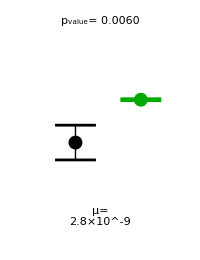

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_no_lag_Pregrowth.png

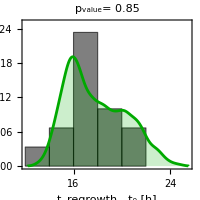

KS-test p-value: 0.852633

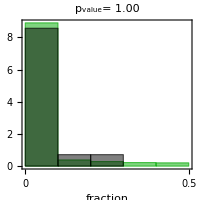

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.890683

```mathematica
simdist=Table[Import["models\\CIP_mult\\distribution_fixed_mu_2strains_mult_mutants_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_mult_allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_mult_allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_mult_allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult"]

args=Table[
{"preexist_res_2strains_mult_alleles_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 20 13 preexist_res_2strains_mult_alleles_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_mult_alleles_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1

0

20

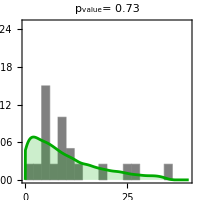

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_mult\\strains_preexist_res_2strains_mult_alleles_"<>mutrate<>"_CIP",strains,alleles,NotebookDirectory[]<>"\\figures\\CIP_mult_allele_no_lag_Nmut.png"]
```

## Now the same model but with filamentation:

### Long - term experiment

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];

LBrates
CIPrates

mutrate="2.8e-9";  
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};

Export[NotebookDirectory[]<>"\\models\\CIP_filament_mult\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_mult"]

args=Table[
{"fixed_mu_2strains_mult_mutants_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament_mult

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 32 13 fixed_mu_2strains_mult_mutants_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_mult_mutants_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_mult_mutants_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_mult_mutants_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_mult_mutants_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_mult_mutants_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_mult_mutants_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_mult_mutants_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_mult_mutants_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_mult_mutants_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_mult_mutants_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_mult_mutants_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_mult_mutants_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_mult_mutants_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_mult_mutants_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_mult_mutants_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_mult_mutants_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_mult_mutants_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_mult_mutants_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_mult_mutants_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_mult_mutants_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_mult_mutants_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_mult_mutants_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_23.dat 0.1 fixed_mu_2strains_mult_mutants_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_24.dat 0.1 fixed_mu_2strains_mult_mutants_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_25.dat 0.1 fixed_mu_2strains_mult_mutants_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_26.dat 0.1 fixed_mu_2strains_mult_mutants_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_27.dat 0.1 fixed_mu_2strains_mult_mutants_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_28.dat 0.1 fixed_mu_2strains_mult_mutants_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_29.dat 0.1 fixed_mu_2strains_mult_mutants_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_30.dat 0.1 fixed_mu_2strains_mult_mutants_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_31.dat 0.1 fixed_mu_2strains_mult_mutants_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_32.dat 0.1

0

0.474167

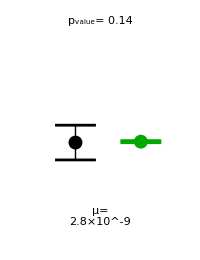

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_mult_allele_no_lag_Pregrowth.png

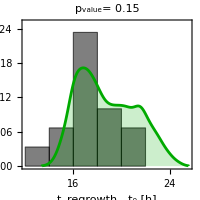

KS-test p-value: 0.149816

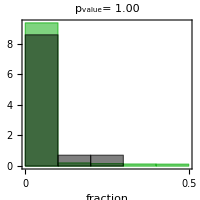

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.93516

```mathematica
simdist=Table[Import["models\\CIP_filament_mult\\distribution_fixed_mu_2strains_mult_mutants_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_filam_mult_allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_filam_mult_allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_filam_mult_allele_no_lag_LBS.png"]
```

## Many resistant alleles. Different mutation probabilities. No lag. Mixed strains AD30 and AD30YFP.

### Long - term experiment

{{gyrA S83L,0.35},{gyrA D87N,0.35},{gyrA D87Y,0.13},{gyrA D87G,0.21},{gyrA G81D,0.35},{gyrA S111Y,0.13},{gyrB S464F,0.35},{gyrB G429V,0.13},{gyrB S463P,0.21}}

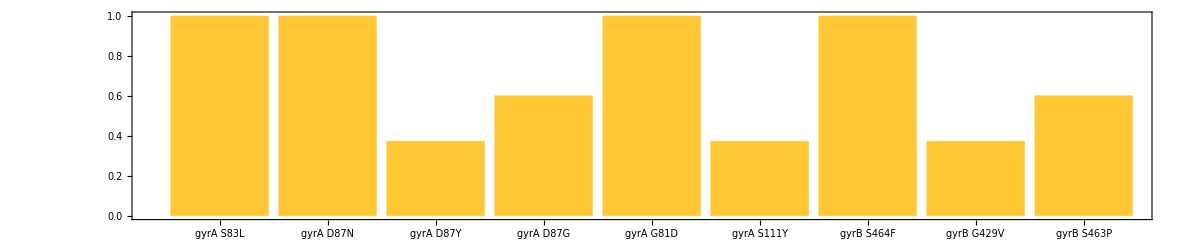

```mathematica
mutexpfreqs=Import["Gyrase_SNP_summary.xlsx"][[1]][[4;;,{2,5}]]
BarChart[mutexpfreqs[[All,2]]/0.35,ChartLabels->mutexpfreqs[[All,1]],AspectRatio->0.2,ImageSize->1200]
```

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];

mutprobs={#[[1]],mutexpfreqs[[Position[mutexpfreqs[[All,1]],#[[1]]][[1,1]],2]]}&/@allrates
DumpSave[NotebookDirectory[]<>"\\CIP_mult_alleles_probs.mx",mutprobs];

LBrates
CIPrates

mutrate="2.8e-9"; 

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}

{{gyrA D87N,0.35},{gyrA G81D,0.35},{gyrA D87Y,0.13},{gyrA D87G,0.21},{gyrB S464F,0.35},{gyrB G429V,0.13},{gyrB S463P,0.21},{gyrA S111Y,0.13},{gyrA S83L,0.35}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_diffp"]

(*Do[
name="START \" \" "<>cmdpars<>" \""<>NotebookDirectory[]<>"\\models\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe\" fixed_mu_mult_strains_"<>ToString[nn]<>" "<>ToString[vols[[nn]]]<>" "<>ToString[odinis[[nn]]]<>" "<>ToString[ainjs[[nn]]]<>" "<>ToString[tends[[nn]]]<>" "<>ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]]<>" "<>ToString[odcrit dilf 0.5]<>noreps<>ToString[mu,CForm]<>" "<>ToString[mu,CForm]<>" "<>ToString[dilf]<>" "<>("input_params_"<>ToString[nn]<>".dat")<>" 0.1 "; (* tolerance *)
Print[name];
Run[name]
,{nn,Length[vols]}]*)

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe 32 13 fixed_mu_mult_strains_1 25.15 0.00303325 4.98706 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat 0.1 fixed_mu_mult_strains_2 25.44 0.00245629 5.06631 30.1147 22.0496 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat 0.1 fixed_mu_mult_strains_3 25.04 0.00289168 4.92292 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat 0.1 fixed_mu_mult_strains_4 26.45 0.00275821 5.00725 30.1147 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat 0.1 fixed_mu_mult_strains_5 25.04 0.00307255 4.85883 26.8178 20.3132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat 0.1 fixed_mu_mult_strains_6 25.56 0.00320347 5.00286 26.8178 21.9364 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat 0.1 fixed_mu_mult_strains_7 24.44 0.00357921 4.87219 26.8178 22.7454 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat 0.1 fixed_mu_mult_strains_8 26.45 0.00320179 4.89711 26.8178 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat 0.1 fixed_mu_mult_strains_9 24.69 0.00310924 4.96761 27.0042 21.7159 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat 0.1 fixed_mu_mult_strains_10 24.97 0.00301076 5.13422 27.0042 24.4248 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat 0.1 fixed_mu_mult_strains_11 24.14 0.0026854 5.01689 27.0042 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat 0.1 fixed_mu_mult_strains_12 25.59 0.00268205 5.05589 27.0043 21.5132 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat 0.1 fixed_mu_mult_strains_13 25.18 0.0027676 5.47 28.5756 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat 0.1 fixed_mu_mult_strains_14 25.87 0.00270966 5.36681 28.5756 22.553 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat 0.1 fixed_mu_mult_strains_15 24.14 0.00289531 5.47883 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat 0.1 fixed_mu_mult_strains_16 25.77 0.00284325 5.22344 28.5758 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat 0.1 fixed_mu_mult_strains_17 25.72 0.00270866 5.12972 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat 0.1 fixed_mu_mult_strains_18 25.84 0.00239707 5.43678 28.5297 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat 0.1 fixed_mu_mult_strains_19 26.37 0.00274375 4.89842 28.5297 23.7273 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat 0.1 fixed_mu_mult_strains_20 27.82 0.00284187 4.54761 28.5297 19.657 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat 0.1 fixed_mu_mult_strains_21 25.9 0.00364933 5.26286 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_21.dat 0.1 fixed_mu_mult_strains_22 25.62 0.00289417 5.39611 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_22.dat 0.1 fixed_mu_mult_strains_23 26.38 0.00272181 4.97361 29.3347 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_23.dat 0.1 fixed_mu_mult_strains_24 27.23 0.00316891 4.51994 29.3347 23.9676 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_24.dat 0.1 fixed_mu_mult_strains_25 25.74 0.00275783 5.46483 28.26 27.4156 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_25.dat 0.1 fixed_mu_mult_strains_26 25.28 0.00245877 5.86117 28.26 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_26.dat 0.1 fixed_mu_mult_strains_27 25.65 0.0036443 5.11125 28.26 21.3304 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_27.dat 0.1 fixed_mu_mult_strains_28 26.52 0.00233044 4.89978 28.26 18.369 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_28.dat 0.1 fixed_mu_mult_strains_29 25.58 0.00429194 4.61986 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_29.dat 0.1 fixed_mu_mult_strains_30 26.38 0.0040433 4.50967 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_30.dat 0.1 fixed_mu_mult_strains_31 25.19 0.00515296 4.43681 28.7853 30 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_31.dat 0.1 fixed_mu_mult_strains_32 25.44 0.00364409 4.47128 28.7853 26.0315 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_32.dat 0.1

0

0.691099

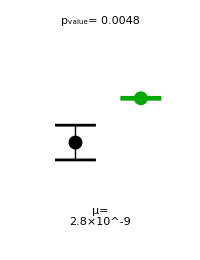

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_diffP_Pregrowth.png

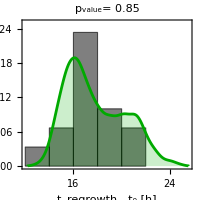

KS-test p-value: 0.853366

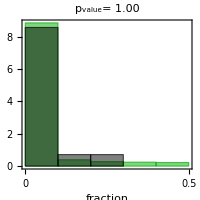

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.885628

```mathematica
simdist=Table[Import["models\\CIP_mult_diffp\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_mult_allele_diffP_Pregrowth.png"]
RegrowtTimeDistribution["CIP_mult_allele_diffP_Tregrowth.png"]
LeastAbundantStrain["CIP_mult_allele_diffP_LBS.png"]
```

### Short - term experiment:

```mathematica
mutrate="2.8e-9";
```

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births2[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

2

9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_diffp"]

(*Do[
name="START \" \" "<>cmdpars<>" \""<>NotebookDirectory[]<>"\\models\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe\" preexist_res_2strains_mult_allele_"<>mutrate<>"_CIP"<>ToString[nn]<>" "<>ToString[vols2[[nn]]]<>" "<>ToString[odinis2[[nn]]]<>" "<>ToString[100]<>" "<>ToString[tends2[[nn]]]<>" "<>ToString[100]<>" "<>ToString[odcrit2 dilf2 0.5]<>noreps<>ToString[mu,CForm]<>" "<>ToString[mu,CForm]<>"  "<>ToString[dilf2]<>" "<>("input_params_"<>ToString[nn]<>".dat")<>" 0.1 "; (* tolerance *)
Print[name];
Run[name]
,{nn,Length[births2]}]*)

args=Table[
{"preexist_res_2strains_mult_allele_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]


SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe 20 13 preexist_res_2strains_mult_allele_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 preexist_res_2strains_mult_allele_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1

0

20

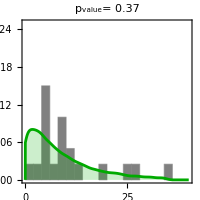

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_diffP_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_mult_diffp\\strains_preexist_res_2strains_mult_allele_"<>mutrate<>"_CIP",strains,alleles,NotebookDirectory[]<>"\\figures\\CIP_mult_allele_diffP_Nmut.png"]
```

## Phenotypic lag model for CIP. One resistant allele. Mixed strains AD30 and AD30YFP.

```mathematica
mutrate="2.8e-9";  (* this value gives a good fit to short-term exp data *)
lagrate="0.05" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.2; (* this must be experimentally chosen to give the best fit *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
(*it=If[birthsres[[nn,1]]>0,birthsres[[nn,1]],births[[nn,1]]]{{1,1},{0.5,0.5}};*)
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{intgrfraction,intgrfraction}}; 
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\CIP_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

2.8×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_lag"]

args=Table[
{"fixed_mu_2strains_lag_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_lag

0.449109

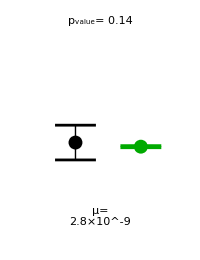

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_2allele_lag_Pregrowth.png

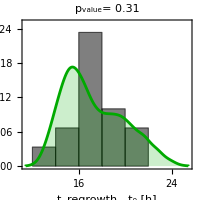

KS-test p-value: 0.314765

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_lag_params.png

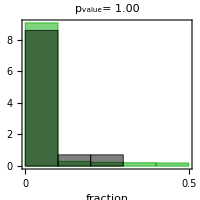

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.905093

```mathematica
simdist=Table[Import["models\\CIP_lag\\distribution_fixed_mu_2strains_lag_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_2allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_2allele_lag_Tregrowth.png"]
Export[NotebookDirectory[]<>"\\figures\\CIP_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
LeastAbundantStrain["CIP_2allele_lag_LBS.png"]
```

### This procedure finds the optimal ω and q to get best combined p-value. The values obtained have to be manually inputted in the simulation above.

```mathematica
Clear[RunOnce2,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce2[ω_?NumericQ,q_?NumericQ]:=RunOnce2[ω,q]=Module[{pval1,pval2,pval3,fractions,simcfus,simdist,tmp,psurv,psurvexp,ret,processes},
(*Return[ω^2+q^2]*)
strains=2;alleles=1;
BlockRandom[Do[
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{Abs[q],Abs[q]}}; 
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
Export[NotebookDirectory[]<>"\\models\\CIP_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123];
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\CIP_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

2.8×10^-9

```mathematica
RunOnce2[0.05,0.3]
```

ω= 0.05 q =0.3 fun=-0.109903

-0.109903

```mathematica
fits=Table[{ω,q,RunOnce2[ω,q]},{ω,0.05,0.3,0.05},{q,0,0.6,0.1}]
```

ω= 0.05 q =0. fun=2.9977

ω= 0.05 q =0.1 fun=-0.0754238

ω= 0.05 q =0.2 fun=-0.135669

ω= 0.05 q =0.4 fun=-0.0427948

ω= 0.05 q =0.5 fun=-0.00561582

ω= 0.05 q =0.6 fun=-0.000257793

ω= 0.1 q =0. fun=5.50354

ω= 0.1 q =0.1 fun=1.72017

ω= 0.1 q =0.2 fun=-0.0467567

ω= 0.1 q =0.3 fun=-0.0171787

ω= 0.1 q =0.4 fun=-0.00367806

ω= 0.1 q =0.5 fun=-0.000258299

ω= 0.1 q =0.6 fun=-0.0000131085

ω= 0.15 q =0. fun=7.79314

ω= 0.15 q =0.1 fun=5.75332

ω= 0.15 q =0.2 fun=1.12488

ω= 0.15 q =0.3 fun=-0.00234825

ω= 0.15 q =0.4 fun=-0.000453988

ω= 0.15 q =0.5 fun=-0.0000419294

ω= 0.15 q =0.6 fun=-8.16455×10^-6

ω= 0.2 q =0. fun=7.85223

ω= 0.2 q =0.1 fun=6.38033

ω= 0.2 q =0.2 fun=1.89674

ω= 0.2 q =0.3 fun=4.90128

ω= 0.2 q =0.4 fun=-0.0000988631

ω= 0.2 q =0.5 fun=3.20252

ω= 0.2 q =0.6 fun=3.86371

ω= 0.25 q =0. fun=8.06031

ω= 0.25 q =0.1 fun=5.34179

ω= 0.25 q =0.2 fun=7.34815

ω= 0.25 q =0.3 fun=5.79563

ω= 0.25 q =0.4 fun=5.0014

ω= 0.25 q =0.5 fun=5.64404

ω= 0.25 q =0.6 fun=6.14635

ω= 0.3 q =0. fun=8.89131

ω= 0.3 q =0.1 fun=7.16073

ω= 0.3 q =0.2 fun=6.35829

ω= 0.3 q =0.3 fun=6.18776

ω= 0.3 q =0.4 fun=6.48915

ω= 0.3 q =0.5 fun=7.04858

ω= 0.3 q =0.6 fun=7.25666

{{{0.05,0.,2.9977},{0.05,0.1,-0.0754238},{0.05,0.2,-0.135669},{0.05,0.3,-0.109903},{0.05,0.4,-0.0427948},{0.05,0.5,-0.00561582},{0.05,0.6,-0.000257793}},{{0.1,0.,5.50354},{0.1,0.1,1.72017},{0.1,0.2,-0.0467567},{0.1,0.3,-0.0171787},{0.1,0.4,-0.00367806},{0.1,0.5,-0.000258299},{0.1,0.6,-0.0000131085}},{{0.15,0.,7.79314},{0.15,0.1,5.75332},{0.15,0.2,1.12488},{0.15,0.3,-0.00234825},{0.15,0.4,-0.000453988},{0.15,0.5,-0.0000419294},{0.15,0.6,-8.16455×10^-6}},{{0.2,0.,7.85223},{0.2,0.1,6.38033},{0.2,0.2,1.89674},{0.2,0.3,4.90128},{0.2,0.4,-0.0000988631},{0.2,0.5,3.20252},{0.2,0.6,3.86371}},{{0.25,0.,8.06031},{0.25,0.1,5.34179},{0.25,0.2,7.34815},{0.25,0.3,5.79563},{0.25,0.4,5.0014},{0.25,0.5,5.64404},{0.25,0.6,6.14635}},{{0.3,0.,8.89131},{0.3,0.1,7.16073},{0.3,0.2,6.35829},{0.3,0.3,6.18776},{0.3,0.4,6.48915},{0.3,0.5,7.04858},{0.3,0.6,7.25666}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.05,0.2,-0.135669},{0.05,0.3,-0.109903},{0.05,0.1,-0.0754238},{0.1,0.2,-0.0467567},{0.05,0.4,-0.0427948},{0.1,0.3,-0.0171787},{0.05,0.5,-0.00561582},{0.1,0.4,-0.00367806},{0.15,0.3,-0.00234825},{0.15,0.4,-0.000453988},{0.1,0.5,-0.000258299},{0.05,0.6,-0.000257793},{0.2,0.4,-0.0000988631},{0.15,0.5,-0.0000419294},{0.1,0.6,-0.0000131085},{0.15,0.6,-8.16455×10^-6},{0.15,0.2,1.12488},{0.1,0.1,1.72017},{0.2,0.2,1.89674},{0.05,0.,2.9977},{0.2,0.5,3.20252},{0.2,0.6,3.86371},{0.2,0.3,4.90128},{0.25,0.4,5.0014},{0.25,0.1,5.34179},{0.1,0.,5.50354},{0.25,0.5,5.64404},{0.15,0.1,5.75332},{0.25,0.3,5.79563},{0.25,0.6,6.14635},{0.3,0.3,6.18776},{0.3,0.2,6.35829},{0.2,0.1,6.38033},{0.3,0.4,6.48915},{0.3,0.5,7.04858},{0.3,0.1,7.16073},{0.3,0.6,7.25666},{0.25,0.2,7.34815},{0.15,0.,7.79314},{0.2,0.,7.85223},{0.25,0.,8.06031},{0.3,0.,8.89131}}

The best fit parameters are the first pair in the above output

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it=births2[[nn,1]]{{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\CIP_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_lag"]

args=Table[
{"preexist_res_2strains_1_allele_lag_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 20 14 preexist_res_2strains_1_allele_lag_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 0.05 preexist_res_2strains_1_allele_lag_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1 0.05

0

20

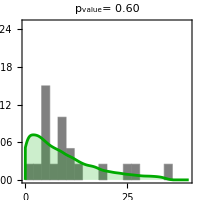

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_2allele_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_lag\\strains_preexist_res_2strains_1_allele_lag_"<>mutrate<>"_CIP",strains,2alleles,NotebookDirectory[]<>"\\figures\\CIP_2allele_lag_Nmut.png"]
```

## Now the same model with filamentation :

```mathematica
mutrate="2.8e-9";  
lagrate="0.15" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.2; (* this must be experimentally chosen to give the best fit *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{intgrfraction,intgrfraction}}; 
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\CIP_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

2.8×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_lag"]

args=Table[
{"fixed_mu_2strains_lag_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament_lag

0.456625

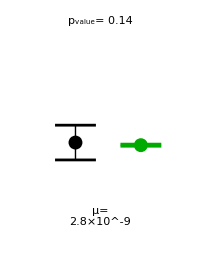

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_2allele_lag_Pregrowth.png

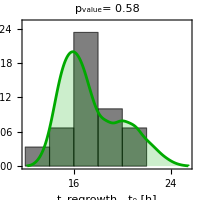

KS-test p-value: 0.57908

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_lag_params.png

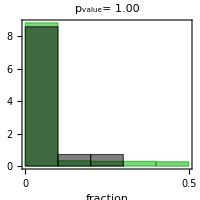

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.88105

```mathematica
simdist=Table[Import["models\\CIP_filament_lag\\distribution_fixed_mu_2strains_lag_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["CIP_filam_2allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_filam_2allele_lag_Tregrowth.png"]
Export[NotebookDirectory[]<>"\\figures\\CIP_filam_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
LeastAbundantStrain["CIP_filam_2allele_lag_LBS.png"]
```

### Now optimize both ω and q. The best-fit values must be the manually entered in the code above.

```mathematica
Clear[RunOnce2,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce2[ω_?NumericQ,q_?NumericQ]:=RunOnce2[ω,q]=Module[{pval1,pval2,pval3,fractions,simcfus,simdist,tmp,psurv,psurvexp,ret,processes},
(*Return[ω^2+q^2]*)
strains=2;alleles=1;
BlockRandom[Do[
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{Abs[q],Abs[q]}}; 
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
Export[NotebookDirectory[]<>"\\models\\CIP_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123];
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\CIP_filament_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

2.8×10^-9

```mathematica
RunOnce2[0.05,0.3]
```

ω= 0.05 q =0.3 fun=-0.0229336

-0.0229336

```mathematica
fits=Table[{ω,q,RunOnce2[ω,q]},{ω,0.05,0.3,0.05},{q,0,0.6,0.1}]
```

ω= 0.05 q =0. fun=-0.00238207

ω= 0.05 q =0.1 fun=-0.00432007

ω= 0.05 q =0.2 fun=-0.00676588

ω= 0.05 q =0.4 fun=-0.058262

ω= 0.05 q =0.5 fun=-0.128984

ω= 0.05 q =0.6 fun=-0.127249

ω= 0.1 q =0. fun=-0.0489762

ω= 0.1 q =0.1 fun=-0.0563589

ω= 0.1 q =0.2 fun=-0.0892234

ω= 0.1 q =0.3 fun=-0.138016

ω= 0.1 q =0.4 fun=-0.140004

ω= 0.1 q =0.5 fun=-0.0974173

ω= 0.1 q =0.6 fun=-0.0627117

ω= 0.15 q =0. fun=-0.115329

ω= 0.15 q =0.1 fun=-0.125822

ω= 0.15 q =0.2 fun=-0.140957

ω= 0.15 q =0.3 fun=-0.132193

ω= 0.15 q =0.4 fun=-0.104785

ω= 0.15 q =0.5 fun=-0.0576336

ω= 0.15 q =0.6 fun=-0.0288562

ω= 0.2 q =0. fun=-0.140652

ω= 0.2 q =0.1 fun=-0.13713

ω= 0.2 q =0.2 fun=-0.115603

ω= 0.2 q =0.3 fun=-0.0962361

ω= 0.2 q =0.4 fun=-0.0624119

ω= 0.2 q =0.5 fun=-0.0470688

ω= 0.2 q =0.6 fun=-0.020325

ω= 0.25 q =0. fun=-0.134479

ω= 0.25 q =0.1 fun=-0.131398

ω= 0.25 q =0.2 fun=-0.0832873

ω= 0.25 q =0.3 fun=-0.0798024

ω= 0.25 q =0.4 fun=-0.0520445

ω= 0.25 q =0.5 fun=-0.0326068

ω= 0.25 q =0.6 fun=-0.0201035

ω= 0.3 q =0. fun=-0.121188

ω= 0.3 q =0.1 fun=-0.104252

ω= 0.3 q =0.2 fun=-0.0741436

ω= 0.3 q =0.3 fun=-0.0552811

ω= 0.3 q =0.4 fun=-0.0386638

ω= 0.3 q =0.5 fun=-0.0193759

ω= 0.3 q =0.6 fun=-0.0122383

{{{0.05,0.,-0.00238207},{0.05,0.1,-0.00432007},{0.05,0.2,-0.00676588},{0.05,0.3,-0.0229336},{0.05,0.4,-0.058262},{0.05,0.5,-0.128984},{0.05,0.6,-0.127249}},{{0.1,0.,-0.0489762},{0.1,0.1,-0.0563589},{0.1,0.2,-0.0892234},{0.1,0.3,-0.138016},{0.1,0.4,-0.140004},{0.1,0.5,-0.0974173},{0.1,0.6,-0.0627117}},{{0.15,0.,-0.115329},{0.15,0.1,-0.125822},{0.15,0.2,-0.140957},{0.15,0.3,-0.132193},{0.15,0.4,-0.104785},{0.15,0.5,-0.0576336},{0.15,0.6,-0.0288562}},{{0.2,0.,-0.140652},{0.2,0.1,-0.13713},{0.2,0.2,-0.115603},{0.2,0.3,-0.0962361},{0.2,0.4,-0.0624119},{0.2,0.5,-0.0470688},{0.2,0.6,-0.020325}},{{0.25,0.,-0.134479},{0.25,0.1,-0.131398},{0.25,0.2,-0.0832873},{0.25,0.3,-0.0798024},{0.25,0.4,-0.0520445},{0.25,0.5,-0.0326068},{0.25,0.6,-0.0201035}},{{0.3,0.,-0.121188},{0.3,0.1,-0.104252},{0.3,0.2,-0.0741436},{0.3,0.3,-0.0552811},{0.3,0.4,-0.0386638},{0.3,0.5,-0.0193759},{0.3,0.6,-0.0122383}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.15,0.2,-0.140957},{0.2,0.,-0.140652},{0.1,0.4,-0.140004},{0.1,0.3,-0.138016},{0.2,0.1,-0.13713},{0.25,0.,-0.134479},{0.15,0.3,-0.132193},{0.25,0.1,-0.131398},{0.05,0.5,-0.128984},{0.05,0.6,-0.127249},{0.15,0.1,-0.125822},{0.3,0.,-0.121188},{0.2,0.2,-0.115603},{0.15,0.,-0.115329},{0.15,0.4,-0.104785},{0.3,0.1,-0.104252},{0.1,0.5,-0.0974173},{0.2,0.3,-0.0962361},{0.1,0.2,-0.0892234},{0.25,0.2,-0.0832873},{0.25,0.3,-0.0798024},{0.3,0.2,-0.0741436},{0.1,0.6,-0.0627117},{0.2,0.4,-0.0624119},{0.05,0.4,-0.058262},{0.15,0.5,-0.0576336},{0.1,0.1,-0.0563589},{0.3,0.3,-0.0552811},{0.25,0.4,-0.0520445},{0.1,0.,-0.0489762},{0.2,0.5,-0.0470688},{0.3,0.4,-0.0386638},{0.25,0.5,-0.0326068},{0.15,0.6,-0.0288562},{0.05,0.3,-0.0229336},{0.2,0.6,-0.020325},{0.25,0.6,-0.0201035},{0.3,0.5,-0.0193759},{0.3,0.6,-0.0122383},{0.05,0.2,-0.00676588},{0.05,0.1,-0.00432007},{0.05,0.,-0.00238207}}

### The best - fit parameters is the first pair from the above list.

```mathematica
ListPlot3D[Flatten[fits,1],PlotRange->{All,0}]
```

-Graphics3D-

## Phenotypic lag model for CIP. Many resistant alleles. No filamentation. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];


allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];

mutprobs={#[[1]],1}&/@allrates[[All]]  (* same mutation probs for all alleles *)

LBrates
CIPrates

mutrate="2.8e-9";  
lagrate="0.15" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.3;  (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction CIPrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}

{{gyrA D87N,1},{gyrA G81D,1},{gyrA D87Y,1},{gyrA D87G,1},{gyrB S464F,1},{gyrB G429V,1},{gyrB S463P,1},{gyrA S111Y,1},{gyrA S83L,1}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag"]

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_lag

### Import and display results:

```mathematica
Style["μ="<>mutrate<>"\nω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->24]
```

μ=2.8e-9
ω=0.15
q=0.3

0.472474

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_params.png

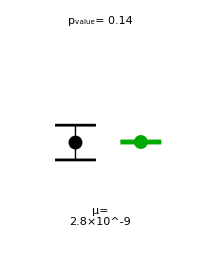

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_Pregrowth.png

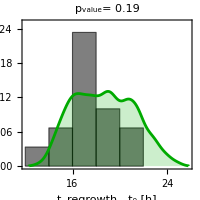

KS-test p-value: 0.187208

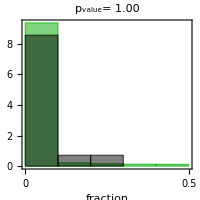

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.937613

```mathematica
simdist=Table[Import["models\\CIP_mult_lag\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\CIP_mult_allele_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["CIP_mult_allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_mult_allele_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_mult_allele_lag_LBS.png"]
```

### Optimize ω and q to get best fit for the combined p-values. The values obtained must be manually copied to the code above that runs the model.

```mathematica
Clear[RunOnce6,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce6[ω_?NumericQ,q_?NumericQ]:=RunOnce6[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[Abs[q] CIPrates[[i]],{strains}],{i,alleles}]]};
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}];
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\CIP_mult_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

2.8×10^-9

```mathematica
fits=Table[{ω,q,RunOnce6[ω,q]},{ω,0.05,0.3,0.05},{q,0,0.6,0.1}]
```

ω= 0.05 q =0. fun=4.54139

ω= 0.05 q =0.1 fun=6.64396

ω= 0.05 q =0.2 fun=7.57405

ω= 0.05 q =0.3 fun=3.96107

ω= 0.05 q =0.4 fun=8.1931

ω= 0.05 q =0.5 fun=6.62234

ω= 0.05 q =0.6 fun=8.18682

ω= 0.1 q =0. fun=-0.022294

ω= 0.1 q =0.1 fun=-0.0330046

ω= 0.1 q =0.2 fun=-0.0784759

ω= 0.1 q =0.3 fun=-0.109217

ω= 0.1 q =0.4 fun=-0.139534

ω= 0.1 q =0.5 fun=0.595447

ω= 0.1 q =0.6 fun=-0.0885

ω= 0.15 q =0. fun=-0.0655687

ω= 0.15 q =0.1 fun=-0.0942777

ω= 0.15 q =0.2 fun=-0.135063

ω= 0.15 q =0.3 fun=-0.141018

ω= 0.15 q =0.4 fun=-0.121949

ω= 0.15 q =0.5 fun=-0.0814953

ω= 0.15 q =0.6 fun=-0.0623798

ω= 0.2 q =0. fun=-0.106364

ω= 0.2 q =0.1 fun=-0.123111

ω= 0.2 q =0.2 fun=-0.138855

ω= 0.2 q =0.3 fun=-0.132679

ω= 0.2 q =0.4 fun=-0.0872669

ω= 0.2 q =0.5 fun=-0.0690268

ω= 0.2 q =0.6 fun=-0.0451593

ω= 0.25 q =0. fun=-0.133583

ω= 0.25 q =0.1 fun=-0.139295

ω= 0.25 q =0.2 fun=-0.13438

ω= 0.25 q =0.3 fun=-0.0987851

ω= 0.25 q =0.4 fun=-0.0746673

ω= 0.25 q =0.5 fun=-0.0616943

ω= 0.25 q =0.6 fun=-0.0349637

ω= 0.3 q =0. fun=-0.140914

ω= 0.3 q =0.1 fun=-0.137705

ω= 0.3 q =0.2 fun=-0.121733

ω= 0.3 q =0.3 fun=-0.0984103

ω= 0.3 q =0.4 fun=-0.0643586

ω= 0.3 q =0.5 fun=-0.0368998

ω= 0.3 q =0.6 fun=-0.0238106

{{{0.05,0.,4.54139},{0.05,0.1,6.64396},{0.05,0.2,7.57405},{0.05,0.3,3.96107},{0.05,0.4,8.1931},{0.05,0.5,6.62234},{0.05,0.6,8.18682}},{{0.1,0.,-0.022294},{0.1,0.1,-0.0330046},{0.1,0.2,-0.0784759},{0.1,0.3,-0.109217},{0.1,0.4,-0.139534},{0.1,0.5,0.595447},{0.1,0.6,-0.0885}},{{0.15,0.,-0.0655687},{0.15,0.1,-0.0942777},{0.15,0.2,-0.135063},{0.15,0.3,-0.141018},{0.15,0.4,-0.121949},{0.15,0.5,-0.0814953},{0.15,0.6,-0.0623798}},{{0.2,0.,-0.106364},{0.2,0.1,-0.123111},{0.2,0.2,-0.138855},{0.2,0.3,-0.132679},{0.2,0.4,-0.0872669},{0.2,0.5,-0.0690268},{0.2,0.6,-0.0451593}},{{0.25,0.,-0.133583},{0.25,0.1,-0.139295},{0.25,0.2,-0.13438},{0.25,0.3,-0.0987851},{0.25,0.4,-0.0746673},{0.25,0.5,-0.0616943},{0.25,0.6,-0.0349637}},{{0.3,0.,-0.140914},{0.3,0.1,-0.137705},{0.3,0.2,-0.121733},{0.3,0.3,-0.0984103},{0.3,0.4,-0.0643586},{0.3,0.5,-0.0368998},{0.3,0.6,-0.0238106}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.15,0.3,-0.141018},{0.3,0.,-0.140914},{0.1,0.4,-0.139534},{0.25,0.1,-0.139295},{0.2,0.2,-0.138855},{0.3,0.1,-0.137705},{0.15,0.2,-0.135063},{0.25,0.2,-0.13438},{0.25,0.,-0.133583},{0.2,0.3,-0.132679},{0.2,0.1,-0.123111},{0.15,0.4,-0.121949},{0.3,0.2,-0.121733},{0.1,0.3,-0.109217},{0.2,0.,-0.106364},{0.25,0.3,-0.0987851},{0.3,0.3,-0.0984103},{0.15,0.1,-0.0942777},{0.1,0.6,-0.0885},{0.2,0.4,-0.0872669},{0.15,0.5,-0.0814953},{0.1,0.2,-0.0784759},{0.25,0.4,-0.0746673},{0.2,0.5,-0.0690268},{0.15,0.,-0.0655687},{0.3,0.4,-0.0643586},{0.15,0.6,-0.0623798},{0.25,0.5,-0.0616943},{0.2,0.6,-0.0451593},{0.3,0.5,-0.0368998},{0.25,0.6,-0.0349637},{0.1,0.1,-0.0330046},{0.3,0.6,-0.0238106},{0.1,0.,-0.022294},{0.1,0.5,0.595447},{0.05,0.3,3.96107},{0.05,0.,4.54139},{0.05,0.5,6.62234},{0.05,0.1,6.64396},{0.05,0.2,7.57405},{0.05,0.6,8.18682},{0.05,0.4,8.1931}}

The first pair of values is the best - fit parameters .

### Short - term experiment:

```mathematica
(* these parameters should not affect the outcome as long as intgrfraction>0 because they do not matter for short-term experiments *)
lagrate="0.15" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.3;  (* this must be experimentally chosen to give the best fit *)
```

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births2[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction CIPrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

2

9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag"]

args=Table[
{"preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 20 14 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 0.15 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1 0.15

0

20

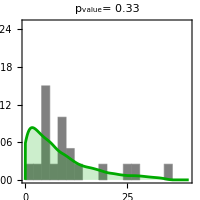

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_mult_lag\\strains_preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_CIP",strains,2alleles,NotebookDirectory[]<>"\\figures\\CIP_mult_allele_lag_Nmut.png"]
```

## Now the same model with filamentation: phenotypic lag, many resistant alleles. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];

mutprobs={#[[1]],1}&/@allrates[[All]]  (* same mutation probs for all alleles *)

LBrates
CIPrates

mutrate="2.8e-9";  
lagrate="0.55" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.5; (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction CIPrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_filament_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}

{{gyrA D87N,1},{gyrA G81D,1},{gyrA D87Y,1},{gyrA D87G,1},{gyrB S464F,1},{gyrB G429V,1},{gyrB S463P,1},{gyrA S111Y,1},{gyrA S83L,1}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_mult_lag"]

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_filament_mult_lag

0.445534

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_mult_allele_lag_params.png

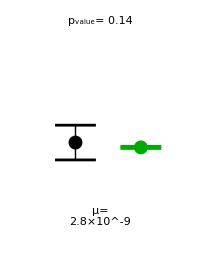

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_filam_mult_allele_lag_Pregrowth.png

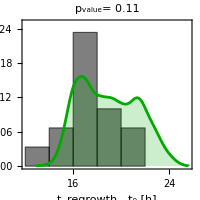

KS-test p-value: 0.107045

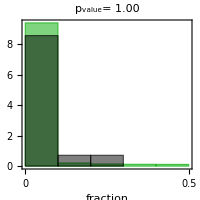

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.940807

```mathematica
simdist=Table[Import["models\\CIP_filament_mult_lag\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\CIP_filam_mult_allele_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["CIP_filam_mult_allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["CIP_filam_mult_allele_lag_Tregrowth.png"]
LeastAbundantStrain["CIP_filam_mult_allele_lag_LBS.png"]
```

### Optimize omega and q (intermediate growth rate) to get best fit for the combined p-values.

```mathematica
Clear[RunOnce6,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce6[ω_?NumericQ,q_?NumericQ]:=RunOnce6[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[Abs[q] CIPrates[[i]],{strains}],{i,alleles}]]};
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_filament_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}];
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_filament_mult_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\CIP_filament_mult_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

2.8×10^-9

```mathematica
fits=Table[{ω,q,RunOnce6[ω,q]},{ω,0.35,0.6,0.05},{q,0,0.6,0.1}]
```

ω= 0.35 q =0. fun=1.1443

ω= 0.35 q =0.1 fun=1.91359

ω= 0.35 q =0.2 fun=2.41262

ω= 0.35 q =0.3 fun=2.41037

ω= 0.35 q =0.4 fun=2.37469

ω= 0.35 q =0.5 fun=2.21784

ω= 0.35 q =0.6 fun=2.11735

ω= 0.4 q =0. fun=-0.0496943

ω= 0.4 q =0.1 fun=1.71175

ω= 0.4 q =0.2 fun=1.73589

ω= 0.4 q =0.3 fun=1.01604

ω= 0.4 q =0.4 fun=3.6558

ω= 0.4 q =0.5 fun=1.56979

ω= 0.4 q =0.6 fun=0.27981

ω= 0.45 q =0. fun=0.501687

ω= 0.45 q =0.1 fun=1.33203

ω= 0.45 q =0.2 fun=1.02603

ω= 0.45 q =0.3 fun=1.46536

ω= 0.45 q =0.4 fun=2.69654

ω= 0.45 q =0.5 fun=0.195628

ω= 0.45 q =0.6 fun=0.477944

ω= 0.5 q =0. fun=-0.0272557

ω= 0.5 q =0.1 fun=0.8083

ω= 0.5 q =0.2 fun=0.377616

ω= 0.5 q =0.3 fun=-0.108138

ω= 0.5 q =0.4 fun=1.27959

ω= 0.5 q =0.5 fun=0.00822332

ω= 0.5 q =0.6 fun=-0.133907

ω= 0.55 q =0. fun=0.0293349

ω= 0.55 q =0.1 fun=-0.096954

ω= 0.55 q =0.2 fun=1.05461

ω= 0.55 q =0.3 fun=-0.113031

ω= 0.55 q =0.4 fun=-0.120049

ω= 0.55 q =0.5 fun=-0.135677

ω= 0.55 q =0.6 fun=0.3536

ω= 0.6 q =0. fun=-0.0870555

ω= 0.6 q =0.1 fun=-0.0997986

ω= 0.6 q =0.2 fun=-0.0995182

ω= 0.6 q =0.3 fun=-0.119075

ω= 0.6 q =0.4 fun=3.31804

ω= 0.6 q =0.5 fun=-0.134678

ω= 0.6 q =0.6 fun=0.407952

{{{0.35,0.,1.1443},{0.35,0.1,1.91359},{0.35,0.2,2.41262},{0.35,0.3,2.41037},{0.35,0.4,2.37469},{0.35,0.5,2.21784},{0.35,0.6,2.11735}},{{0.4,0.,-0.0496943},{0.4,0.1,1.71175},{0.4,0.2,1.73589},{0.4,0.3,1.01604},{0.4,0.4,3.6558},{0.4,0.5,1.56979},{0.4,0.6,0.27981}},{{0.45,0.,0.501687},{0.45,0.1,1.33203},{0.45,0.2,1.02603},{0.45,0.3,1.46536},{0.45,0.4,2.69654},{0.45,0.5,0.195628},{0.45,0.6,0.477944}},{{0.5,0.,-0.0272557},{0.5,0.1,0.8083},{0.5,0.2,0.377616},{0.5,0.3,-0.108138},{0.5,0.4,1.27959},{0.5,0.5,0.00822332},{0.5,0.6,-0.133907}},{{0.55,0.,0.0293349},{0.55,0.1,-0.096954},{0.55,0.2,1.05461},{0.55,0.3,-0.113031},{0.55,0.4,-0.120049},{0.55,0.5,-0.135677},{0.55,0.6,0.3536}},{{0.6,0.,-0.0870555},{0.6,0.1,-0.0997986},{0.6,0.2,-0.0995182},{0.6,0.3,-0.119075},{0.6,0.4,3.31804},{0.6,0.5,-0.134678},{0.6,0.6,0.407952}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.55,0.5,-0.135677},{0.6,0.5,-0.134678},{0.5,0.6,-0.133907},{0.55,0.4,-0.120049},{0.6,0.3,-0.119075},{0.55,0.3,-0.113031},{0.5,0.3,-0.108138},{0.6,0.1,-0.0997986},{0.6,0.2,-0.0995182},{0.55,0.1,-0.096954},{0.6,0.,-0.0870555},{0.4,0.,-0.0496943},{0.5,0.,-0.0272557},{0.5,0.5,0.00822332},{0.55,0.,0.0293349},{0.45,0.5,0.195628},{0.4,0.6,0.27981},{0.55,0.6,0.3536},{0.5,0.2,0.377616},{0.6,0.6,0.407952},{0.45,0.6,0.477944},{0.45,0.,0.501687},{0.5,0.1,0.8083},{0.4,0.3,1.01604},{0.45,0.2,1.02603},{0.55,0.2,1.05461},{0.35,0.,1.1443},{0.5,0.4,1.27959},{0.45,0.1,1.33203},{0.45,0.3,1.46536},{0.4,0.5,1.56979},{0.4,0.1,1.71175},{0.4,0.2,1.73589},{0.35,0.1,1.91359},{0.35,0.6,2.11735},{0.35,0.5,2.21784},{0.35,0.4,2.37469},{0.35,0.3,2.41037},{0.35,0.2,2.41262},{0.45,0.4,2.69654},{0.6,0.4,3.31804},{0.4,0.4,3.6558}}

## Phenotypic lag model for CIP. Many resistant alleles. Different mutation probabilities. No filamentation. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
mutexpfreqs=Import["Gyrase_SNP_summary.xlsx"][[1]][[4;;,{2,5}]]
BarChart[mutexpfreqs[[All,2]]/0.35,ChartLabels->mutexpfreqs[[All,1]],AspectRatio->0.2,ImageSize->1200]
```

{{gyrA S83L,0.35},{gyrA D87N,0.35},{gyrA D87Y,0.13},{gyrA D87G,0.21},{gyrA G81D,0.35},{gyrA S111Y,0.13},{gyrB S464F,0.35},{gyrB G429V,0.13},{gyrB S463P,0.21}}

-Graphics-

```mathematica
tmp=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
CIPrates=allrates[[All,3]];


mutprobs={#[[1]],mutexpfreqs[[Position[mutexpfreqs[[All,1]],#[[1]]][[1,1]],2]]}&/@allrates

LBrates
CIPrates

mutrate="2.8e-9";  
lagrate="0.3" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.0;  (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction CIPrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{gyrA D87N,1.91654,1.43438},{gyrA G81D,1.66216,1.23893},{gyrA D87Y,1.85083,1.53978},{gyrA D87G,1.98136,1.39731},{gyrB S464F,1.83286,1.05029},{gyrB G429V,1.24441,1.12944},{gyrB S463P,1.62962,1.763},{gyrA S111Y,1.85954,0.876618},{gyrA S83L,1.84706,1.67539}}

{{gyrA D87N,0.35},{gyrA G81D,0.35},{gyrA D87Y,0.13},{gyrA D87G,0.21},{gyrB S464F,0.35},{gyrB G429V,0.13},{gyrB S463P,0.21},{gyrA S111Y,0.13},{gyrA S83L,0.35}}

{1.91654,1.66216,1.85083,1.98136,1.83286,1.24441,1.62962,1.85954,1.84706}

{1.43438,1.23893,1.53978,1.39731,1.05029,1.12944,1.763,0.876618,1.67539}

2.8×10^-9

2

9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp"]

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_lag_diffp

### Process data as usual:

0.479836

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_diffP_params.png

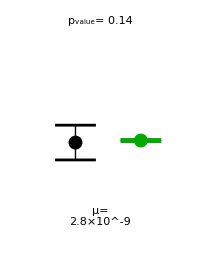

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_diffP_Pregrowth.png

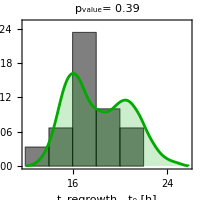

KS-test p-value: 0.394569

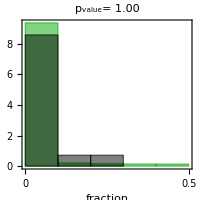

fraction below 0.1 (exp):0.857143

fraction below 0.1 (sim):0.936132

```mathematica
simdist=Table[Import["models\\CIP_mult_lag_diffp\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\CIP_mult_allele_lag_diffP_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["CIP_mult_allele_lag_diffP_Pregrowth.png"]
RegrowtTimeDistribution["CIP_mult_allele_lag_diffP_Tregrowth.png"]
LeastAbundantStrain["CIP_mult_allele_lag_diffP_LBS.png"]
```

### Optimize ω and q (int_growth_rate) to get best fit for the combined p-values.

```mathematica
Clear[RunOnce4,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce4[ω_?NumericQ,q_?NumericQ]:=RunOnce4[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[Abs[q] CIPrates[[i]],{strains}],{i,alleles}]]};
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}];
(*Do[processes=ToString[#]&/@Normal[SystemProcessData[][All,"Program"]];If[AnyTrue[processes,StringContainsQ["turbidostat_evolution"~~__]]==False,Break[]],{st,100}];*)
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp"];

(*Do[
name="START \" \" "<>cmdpars<>" \""<>NotebookDirectory[]<>"\\models\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe\" optimization_"<>ToString[nn]<>" "<>ToString[vols[[nn]]]<>" "<>ToString[odinis[[nn]]]<>" "<>ToString[ainjs[[nn]]]<>" "<>ToString[tends[[nn]]]<>" "<>ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]]<>" "<>ToString[odcrit dilf 0.5]<>" 300 "<>ToString[mu,CForm]<>" "<>ToString[mu,CForm]<>" "<>ToString[dilf]<>" "<>("input_params_"<>ToString[nn]<>".dat")<>" 0.1 "<>ToString[Abs[ω]]; (* tolerance, omega *)
Run[name]
,{nn,Length[births]}];*);

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]](* tolerance, omega *)},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)



SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\CIP_mult_lag_diffp\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

2.8×10^-9

```mathematica
RunOnce4[0.2,0.3]
```

ω= 0.2 q =0.3 fun=-0.124914

-0.124914

```mathematica
fits=Table[{ω,q,RunOnce4[ω,q]},{ω,0.05,0.3,0.05},{q,0,0.5,0.1}]
```

ω= 0.05 q =0. fun=4.79851

ω= 0.05 q =0.1 fun=4.0471

ω= 0.05 q =0.2 fun=-0.00862458

ω= 0.05 q =0.3 fun=6.72775

ω= 0.05 q =0.4 fun=5.00521

ω= 0.05 q =0.5 fun=6.55833

ω= 0.1 q =0. fun=-0.0279252

ω= 0.1 q =0.1 fun=-0.0508368

ω= 0.1 q =0.2 fun=-0.0846644

ω= 0.1 q =0.3 fun=-0.139069

ω= 0.1 q =0.4 fun=-0.140794

ω= 0.1 q =0.5 fun=-0.125368

ω= 0.15 q =0. fun=-0.073036

ω= 0.15 q =0.1 fun=-0.104454

ω= 0.15 q =0.2 fun=-0.135208

ω= 0.15 q =0.3 fun=-0.133341

ω= 0.15 q =0.4 fun=-0.126739

ω= 0.15 q =0.5 fun=-0.0842261

ω= 0.2 q =0. fun=-0.114612

ω= 0.2 q =0.1 fun=-0.138039

ω= 0.2 q =0.2 fun=-0.140445

ω= 0.2 q =0.4 fun=-0.102852

ω= 0.2 q =0.5 fun=-0.0492166

ω= 0.25 q =0. fun=-0.134142

ω= 0.25 q =0.1 fun=-0.140274

ω= 0.25 q =0.2 fun=-0.113073

ω= 0.25 q =0.3 fun=-0.0974737

ω= 0.25 q =0.4 fun=-0.0713881

ω= 0.25 q =0.5 fun=-0.0474625

ω= 0.3 q =0. fun=-0.140809

ω= 0.3 q =0.1 fun=-0.127939

ω= 0.3 q =0.2 fun=-0.0877612

ω= 0.3 q =0.3 fun=-0.084776

ω= 0.3 q =0.4 fun=-0.0530611

ω= 0.3 q =0.5 fun=-0.0269745

{{{0.05,0.,4.79851},{0.05,0.1,4.0471},{0.05,0.2,-0.00862458},{0.05,0.3,6.72775},{0.05,0.4,5.00521},{0.05,0.5,6.55833}},{{0.1,0.,-0.0279252},{0.1,0.1,-0.0508368},{0.1,0.2,-0.0846644},{0.1,0.3,-0.139069},{0.1,0.4,-0.140794},{0.1,0.5,-0.125368}},{{0.15,0.,-0.073036},{0.15,0.1,-0.104454},{0.15,0.2,-0.135208},{0.15,0.3,-0.133341},{0.15,0.4,-0.126739},{0.15,0.5,-0.0842261}},{{0.2,0.,-0.114612},{0.2,0.1,-0.138039},{0.2,0.2,-0.140445},{0.2,0.3,-0.124914},{0.2,0.4,-0.102852},{0.2,0.5,-0.0492166}},{{0.25,0.,-0.134142},{0.25,0.1,-0.140274},{0.25,0.2,-0.113073},{0.25,0.3,-0.0974737},{0.25,0.4,-0.0713881},{0.25,0.5,-0.0474625}},{{0.3,0.,-0.140809},{0.3,0.1,-0.127939},{0.3,0.2,-0.0877612},{0.3,0.3,-0.084776},{0.3,0.4,-0.0530611},{0.3,0.5,-0.0269745}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.3,0.,-0.140809},{0.1,0.4,-0.140794},{0.2,0.2,-0.140445},{0.25,0.1,-0.140274},{0.1,0.3,-0.139069},{0.2,0.1,-0.138039},{0.15,0.2,-0.135208},{0.25,0.,-0.134142},{0.15,0.3,-0.133341},{0.3,0.1,-0.127939},{0.15,0.4,-0.126739},{0.1,0.5,-0.125368},{0.2,0.3,-0.124914},{0.2,0.,-0.114612},{0.25,0.2,-0.113073},{0.15,0.1,-0.104454},{0.2,0.4,-0.102852},{0.25,0.3,-0.0974737},{0.3,0.2,-0.0877612},{0.3,0.3,-0.084776},{0.1,0.2,-0.0846644},{0.15,0.5,-0.0842261},{0.15,0.,-0.073036},{0.25,0.4,-0.0713881},{0.3,0.4,-0.0530611},{0.1,0.1,-0.0508368},{0.2,0.5,-0.0492166},{0.25,0.5,-0.0474625},{0.1,0.,-0.0279252},{0.3,0.5,-0.0269745},{0.05,0.2,-0.00862458},{0.05,0.1,4.0471},{0.05,0.,4.79851},{0.05,0.4,5.00521},{0.05,0.5,6.55833},{0.05,0.3,6.72775}}

### Short - term experiment:

```mathematica
(* these parameters should not affect the outcome as long as intgrfraction>0 because they do not matter for short-term experiments *)
lagrate="0.3" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.0;  (* this must be experimentally chosen to give the best fit *)
```

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births2[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction CIPrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[CIPrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

2.8×10^-9

2

9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp"]

args=Table[
{"preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_CIP"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_mult_lag_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 20 14 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP1 25.5 0.0028813 100 4.98647 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_1.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP2 25.46 0.00238419 100 4.9865 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_2.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP3 24.14 0.00257624 100 4.98653 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_3.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP4 25.09 0.00250156 100 4.98656 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_4.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP5 25.35 0.0021823 100 5.38328 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_5.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP6 25.82 0.00219333 100 5.38331 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_6.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP7 24.14 0.00177883 100 5.38333 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_7.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP8 26.06 0.00191679 100 5.38336 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_8.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP9 24.8 0.00422044 100 4.89047 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_9.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP10 26.09 0.00354104 100 4.8905 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_10.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP11 24.6 0.00388743 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_11.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP12 26.03 0.00388689 100 4.89053 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_12.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP13 24.83 0.00225889 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_13.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP14 25.68 0.00306119 100 4.98378 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_14.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP15 25.1 0.00291718 100 4.98381 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_15.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP16 24.67 0.00254451 100 4.98383 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_16.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP17 24.57 0.00156835 100 5.19553 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_17.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP18 24.14 0.00142162 100 5.19556 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_18.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP19 24.14 0.00201177 100 5.19561 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_19.dat  0.1 0.3 preexist_res_2strains_mult_allele_lag_2.8e-9_CIP20 26.66 0.00167796 100 5.19567 100 0.05 1000 2.8e-9 2.8e-9 0.75 input_params_20.dat  0.1 0.3

0

20

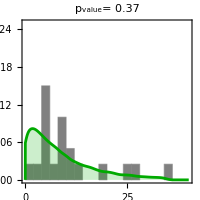

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\CIP_mult_allele_lag_diffP_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\CIP_mult_lag_diffp\\strains_preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_CIP",strains,2alleles,NotebookDirectory[]<>"\\figures\\CIP_mult_allele_lag_diffP_Nmut.png"]
```